## TB NNN

```mathematica
ClearAll["Global`*"];
```

```mathematica
Quit
```

```mathematica
(*Lattice constant*)
a=1.56;    (*look for papers that show this value*)
t=2.7;                            (*t=2.7–2.9 (eV;2.7 is common)*)
Δ=0;
t2A =0.1 ;(*look for papers that show this value*)
t2B =0.1;
(*Δ=0 for graphene and Δ=5.8 for hBN. t=2.9 graphene and t=2.7. a=2.46 for graphene*)
(*Real-space lattice vectors*)
a1=a*{3/2,-Sqrt[3]/2};
a2=a*{3/2,Sqrt[3]/2};
(*Compute area of unit cell*)
area=a1[[1]]*a2[[2]]-a1[[2]]*a2[[1]];
b1=(2*Pi/area)*{a2[[2]],-a2[[1]]};
b2=(2*Pi/area)*{-a1[[2]],a1[[1]]};
delta1=(a1+a2)/3;
delta2=(-2*a1/3+a2/3);
delta3=(a1/3-2*a2/3);
delta4=a1;
delta5=a2;
delta6=-a1;
delta7 = -a2;
delta8=(a2-a1);
delta9=-(a2-a1);
gamma[kx_,ky_]:=Exp[I*(kx*delta1[[1]]+ky*delta1[[2]])]+Exp[I*(kx*delta2[[1]]+ky*delta2[[2]])]+Exp[I*(kx*delta3[[1]]+ky*delta3[[2]])]
gk[kx_,ky_]:=2 (Cos[kx a1[[1]]+ky a1[[2]]]+Cos[kx a2[[1]]+ky a2[[2]]]+Cos[kx (a2-a1)[[1]]+ky (a2-a1)[[2]]]);
H[kx_,ky_]:={{Δ/2+t2A*gk[kx,ky],t*gamma[kx,ky]},{t*Conjugate[gamma[kx,ky]],-Δ/2+t2B*gk[kx,ky]}};
eigenvals[kx_,ky_]:=Sort[Eigenvalues[H[kx,ky]]]
```

## Band Structure - NNN-TB-Biaxial Strain

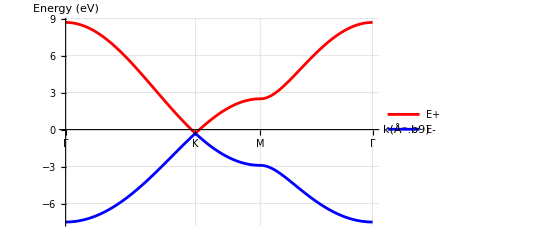

```mathematica
area=a1[[1]]*a2[[2]]-a1[[2]]*a2[[1]];
b1=(2*Pi/area)*{a2[[2]],-a2[[1]]};
b2=(2*Pi/area)*{-a1[[2]],a1[[1]]};

kΓ={0,0};
kK=(1/3)*(b1-b2);
kM=(1/2)*b1;
kPath=Join[Table[(1-s) kΓ+s kK,{s,0,1,0.01}],Table[(1-s) kK+s kM,{s,0,1,0.01}],Table[(1-s) kM+s kΓ,{s,0,1,0.01}]];
kDistances=
Prepend[
Accumulate[
Norm/@Differences[kPath]
],
0
];
bands=eigenvals@@@kPath;
bandsPlus=bands[[All,2]];
bandsMinus=bands[[All,1]];
symmetryPoints={1,Length[kPath]/3,2*Length[kPath]/3,Length[kPath]};
tickPositions=kDistances[[Round[symmetryPoints]]];
tickLabels={"Γ","K","M","Γ"};
ticks=Transpose[{tickPositions,tickLabels}];
bandsPlusData=Transpose[{kDistances,bandsPlus}];
bandsMinusData=Transpose[{kDistances,bandsMinus}];
Show[ListLinePlot[bandsPlusData,Joined->True,PlotStyle->Red,PlotLegends->{"E+"}],ListLinePlot[bandsMinusData,Joined->True,PlotStyle->Blue,PlotLegends->{"E-"}],Ticks->{{{kDistances[[1]],"Γ"},{kDistances[[Length[kPath]/3]],"K"},{kDistances[[2*Length[kPath]/3]],"M"},{kDistances[[Length[kPath]]],"Γ"}},Automatic},AxesLabel->{"k(Å⁻.b9)","Energy (eV)"},GridLines->Automatic,PlotLabel->Style["",16],PlotRange->All,LabelStyle->14]
```

## 3D-Dirac Cone

```mathematica
(*one Dirac point in the Brillouin zone*)
K=(2 b1+b2)/3;
Kx=K[[1]];
Ky=K[[2]];

(*check:the two eigenvalues at K should coincide*)
eigenvals[Kx,Ky]
```

{-0.3,-0.3}

```mathematica
(*local dispersion around K:q=k-K*)
Eminus[qx_,qy_]:=eigenvals[Kx+qx,Ky+qy][[1]];  (*valence band*)
Eplus[qx_,qy_]:=eigenvals[Kx+qx,Ky+qy][[2]];  (*conduction band*)
```

```mathematica
(*size of the patch around K:increase to see higher energies*)qmax=1.0;  (*try 0.8,1.0,1.2 to taste*)

(*lower cone:valence band*)
lowerSurface=Plot3D[Eminus[qx,qy],{qx,-qmax,qmax},{qy,-qmax,qmax},PlotRange->All,PlotPoints->70,MaxRecursion->3,Mesh->None,Exclusions->None,BoundaryStyle->None,ColorFunction->"DeepSeaColors",ColorFunctionScaling->True,PlotStyle->Directive[Opacity[1]],BoxRatios->{1,1,0.6},AxesLabel->(Style[#,14,Bold]&/@{"q_x","q_y","E (eV)"}),LabelStyle->Directive[14],Lighting->"Neutral",PerformanceGoal->"Quality"];

(*upper cone:conduction band,shifted up by a tiny amount to avoid overlap*)
upperSurface=Plot3D[Eplus[qx,qy]+10.^-4,(*tiny shift in energy,visually negligible*){qx,-qmax,qmax},{qy,-qmax,qmax},PlotRange->All,PlotPoints->70,MaxRecursion->3,Mesh->None,Exclusions->None,BoundaryStyle->None,ColorFunction->"DeepSeaColors",ColorFunctionScaling->True,PlotStyle->Directive[Opacity[1]],BoxRatios->{1,1,0.6},AxesLabel->None,Lighting->"Neutral",PerformanceGoal->"Quality"];

DiracConeTwoColorPlot=Show[lowerSurface,upperSurface,ImageSize->Large,AxesLabel->(Style[#,14,Bold]&/@{"","q","E (eV)"})]
```

-Graphics3D-

```mathematica
Quit
```

```mathematica
ClearAll["Global`*"];

(*Upper Dirac cone around K for a given a*)
ClearAll[DiracUpper];
DiracUpper[aVal_?NumericQ]:=Module[{a=aVal,t=2.7,Δ=0,t2A=-0.1,t2B=-0.1,a1,a2,area,b1,b2,delta1,delta2,delta3,gamma,gk,H,eigenvals,K,Kx,Ky},(*lattice geometry for this a*)a1=a {3/2,-Sqrt[3]/2};
a2=a {3/2,Sqrt[3]/2};
area=a1[[1]] a2[[2]]-a1[[2]] a2[[1]];
b1=(2 Pi/area) {a2[[2]],-a2[[1]]};
b2=(2 Pi/area) {-a1[[2]],a1[[1]]};
delta1=(a1+a2)/3;
delta2=(-2 a1+a2)/3;
delta3=(a1-2 a2)/3;
(*nearest-neighbor structure factor*)gamma[kx_,ky_]:=Exp[I (kx delta1[[1]]+ky delta1[[2]])]+Exp[I (kx delta2[[1]]+ky delta2[[2]])]+Exp[I (kx delta3[[1]]+ky delta3[[2]])];
(*next-nearest-neighbor factor*)gk[kx_,ky_]:=2 (Cos[kx a1[[1]]+ky a1[[2]]]+Cos[kx a2[[1]]+ky a2[[2]]]+Cos[kx (a2-a1)[[1]]+ky (a2-a1)[[2]]]);
(*2x2 Bloch Hamiltonian*)H[kx_,ky_]:={{Δ/2+t2A gk[kx,ky],t gamma[kx,ky]},{t Conjugate[gamma[kx,ky]],-Δ/2+t2B gk[kx,ky]}};
eigenvals[kx_,ky_]:=Sort[Eigenvalues[H[kx,ky]]];
(*Dirac point in this Brillouin zone*)K=(2 b1+b2)/3;
{Kx,Ky}=K;
(*return upper band as function of q=k-K*)Function[{qx,qy},eigenvals[Kx+qx,Ky+qy][[2]]]];

(*two values of a: strained*)
aEq=1.36;
aStr=1.56;

EplusEq=DiracUpper[aEq];
EplusStr=DiracUpper[aStr];

qmax=1.0;

coneEq=Plot3D[EplusEq[qx,qy],{qx,-qmax,qmax},{qy,-qmax,qmax},PlotRange->All,Mesh->None,Exclusions->None,BoundaryStyle->None,ColorFunction->"BlueGreenYellow",ColorFunctionScaling->True,PlotStyle->Opacity[0.7],BoxRatios->{1,1,1},PlotPoints->{80,80},MaxRecursion->2,AxesLabel->(Style[#,14,Bold]&/@{"","","E (eV)"})];

coneStr=Plot3D[EplusStr[qx,qy]+10.^-4,{qx,-qmax,qmax},{qy,-qmax,qmax},PlotRange->All,Mesh->None,Exclusions->None,BoundaryStyle->None,ColorFunction->"SolarColors",ColorFunctionScaling->True,PlotStyle->Opacity[1],BoxRatios->{1,1,1},PlotPoints->{80,80},MaxRecursion->2,AxesLabel->None];

Show[coneEq,coneStr,ImageSize->Large]
```

-Graphics3D-

## Fermi velocities a-model

-Graphics-
-Graphics-

```mathematica
(*numerical Fermi velocity from Eplus around q=0*)
ClearAll[FermiSlopeEVAng,FermiVelocityMS];

(*slope dE/dq (in eV·Å) along+qx at qy=0*)
FermiSlopeEVAng[aVal_?NumericQ]:=Module[{Eplus,dq=10.^-3},Eplus=DiracUpper[aVal];(*Eplus[qx,qy] from your code*)(Eplus[dq,0]-Eplus[0,0])/dq   (*one-sided derivative*)];

(*conversion from eV·Å to m/s:1 (eV·Å)≈1.52×10^5 m/s*)
eVAngstromToMS=1.52*10^5;

FermiVelocityMS[aVal_?NumericQ]:=Abs[FermiSlopeEVAng[aVal]]*eVAngstromToMS;
```

```mathematica
FermiSlopeEVAng[1.42]    (*slope in eV·Å*)
FermiVelocityMS[1.42]    (*Fermi velocity in m/s*)

FermiVelocityMS[1.36]
FermiVelocityMS[1.56]
```

5.75055

874083.

837153.

960253.

## TB NNN with t(a) for biaxial compression

```mathematica
Quit
```

```mathematica
ClearAll["Global`*"];

(*---reference parameters and t(a) definition---*)

a0=1.56;    (*equilibrium C–C distance (Angstrom)*)
t0=2.7;     (*nearest-neighbor hopping at a0 (eV)*)
t20=0.1;     (*next-nearest-neighbor hopping at a0 (eV)*)
β=3.37;   (*dimensionless decay parameter from Ribeiro/Pereira*)

tOf[a_]:=t0 Exp[-β (a/a0-1)];   (*distance-dependent t(a)*)
t2Of[a_]:=t20 Exp[-β (a/a0-1)];   (*optional:distance-dependent t2(a)*)

(*---tight-binding model,now using t(a)---*)

a=1.42;    (*you will change this to 1.36,1.49,1.56,etc.*)

Δ=0;

(*Real-space lattice vectors*)
a1=a*{3/2,-Sqrt[3]/2};
a2=a*{3/2,Sqrt[3]/2};

(*Compute area of unit cell*)
area=a1[[1]]*a2[[2]]-a1[[2]]*a2[[1]];

(*Reciprocal lattice vectors*)
b1=(2*Pi/area)*{a2[[2]],-a2[[1]]};
b2=(2*Pi/area)*{-a1[[2]],a1[[1]]};

(*Nearest-neighbor vectors*)
delta1=(a1+a2)/3;
delta2=(-2*a1/3+a2/3);
delta3=(a1/3-2*a2/3);

(*Next-nearest-neighbor vectors*)
delta4=a1;
delta5=a2;
delta6=-a1;
delta7=-a2;
delta8=(a2-a1);
delta9=-(a2-a1);

(*structure factor for nearest neighbors*)
gamma[kx_,ky_]:=Exp[I*(kx*delta1[[1]]+ky*delta1[[2]])]+Exp[I*(kx*delta2[[1]]+ky*delta2[[2]])]+Exp[I*(kx*delta3[[1]]+ky*delta3[[2]])];

(*next-nearest-neighbor factor*)
gk[kx_,ky_]:=2 (Cos[kx a1[[1]]+ky a1[[2]]]+Cos[kx a2[[1]]+ky a2[[2]]]+Cos[kx (a2-a1)[[1]]+ky (a2-a1)[[2]]]);

(*Bloch Hamiltonian with t(a) and t2(a)*)
H[kx_,ky_]:=Module[{t=tOf[a],t2A=t2Of[a],t2B=t2Of[a]},{{Δ/2+t2A*gk[kx,ky],t*gamma[kx,ky]},{t*Conjugate[gamma[kx,ky]],-Δ/2+t2B*gk[kx,ky]}}];

(*sorted eigenvalues*)
eigenvals[kx_,ky_]:=Sort[Eigenvalues[H[kx,ky]]];
```

## Band Structure t(a)

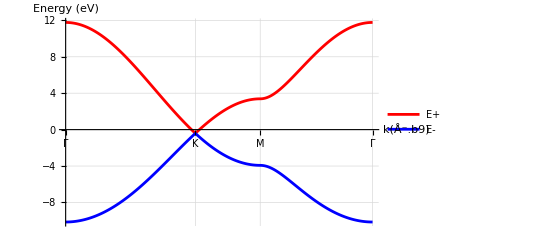

```mathematica
area=a1[[1]]*a2[[2]]-a1[[2]]*a2[[1]];
b1=(2*Pi/area)*{a2[[2]],-a2[[1]]};
b2=(2*Pi/area)*{-a1[[2]],a1[[1]]};

kΓ={0,0};
kK=(1/3)*(b1-b2);
kM=(1/2)*b1;
kPath=Join[Table[(1-s) kΓ+s kK,{s,0,1,0.01}],Table[(1-s) kK+s kM,{s,0,1,0.01}],Table[(1-s) kM+s kΓ,{s,0,1,0.01}]];
kDistances=
Prepend[
Accumulate[
Norm/@Differences[kPath]
],
0
];
bands=eigenvals@@@kPath;
bandsPlus=bands[[All,2]];
bandsMinus=bands[[All,1]];
symmetryPoints={1,Length[kPath]/3,2*Length[kPath]/3,Length[kPath]};
tickPositions=kDistances[[Round[symmetryPoints]]];
tickLabels={"Γ","K","M","Γ"};
ticks=Transpose[{tickPositions,tickLabels}];
bandsPlusData=Transpose[{kDistances,bandsPlus}];
bandsMinusData=Transpose[{kDistances,bandsMinus}];
Show[ListLinePlot[bandsPlusData,Joined->True,PlotStyle->Red,PlotLegends->{"E+"}],ListLinePlot[bandsMinusData,Joined->True,PlotStyle->Blue,PlotLegends->{"E-"}],Ticks->{{{kDistances[[1]],"Γ"},{kDistances[[Length[kPath]/3]],"K"},{kDistances[[2*Length[kPath]/3]],"M"},{kDistances[[Length[kPath]]],"Γ"}},Automatic},AxesLabel->{"k(Å⁻.b9)","Energy (eV)"},GridLines->Automatic,PlotLabel->Style["",16],PlotRange->All,LabelStyle->14]
```

## Dirac cone t(a)

```mathematica
ClearAll["Global`*"];

(*---reference values and distance-dependent hoppings---*)

a0=1.42;    (*equilibrium C–C distance*)
t0=2.7;     (*nearest-neighbor hopping at a0 (eV)*)
t20=-0.1;    (*next-nearest-neighbor hopping at a0 (eV);use sign you prefer*)
β=3.37;   (*decay parameter from strained-graphene tight binding fits*)

tOf[a_]:=t0 Exp[-β (a/a0-1)];   (*t(a)*)
t2Of[a_]:=t20 Exp[-β (a/a0-1)];   (*t2(a),optional same law*)


(*---Upper Dirac cone around K for a given a,now with t(a),t2(a)---*)

ClearAll[DiracUpper];
DiracUpper[aVal_?NumericQ]:=Module[{a=aVal,Δ=0,a1,a2,area,b1,b2,delta1,delta2,delta3,gamma,gk,H,eigenvals,K,Kx,Ky,t,t2A,t2B},(*distance-dependent hoppings*)
t=tOf[a];
t2A=t2Of[a];
t2B=t2Of[a];
(*lattice geometry for this a*)
a1=a {3/2,-Sqrt[3]/2};
a2=a {3/2,Sqrt[3]/2};
area=a1[[1]] a2[[2]]-a1[[2]] a2[[1]];
b1=(2 Pi/area) {a2[[2]],-a2[[1]]};
b2=(2 Pi/area) {-a1[[2]],a1[[1]]};
delta1=(a1+a2)/3;
delta2=(-2 a1+a2)/3;
delta3=(a1-2 a2)/3;
(*nearest-neighbor structure factor*)gamma[kx_,ky_]:=Exp[I (kx delta1[[1]]+ky delta1[[2]])]+Exp[I (kx delta2[[1]]+ky delta2[[2]])]+Exp[I (kx delta3[[1]]+ky delta3[[2]])];
(*next-nearest-neighbor factor*)gk[kx_,ky_]:=2 (Cos[kx a1[[1]]+ky a1[[2]]]+Cos[kx a2[[1]]+ky a2[[2]]]+Cos[kx (a2-a1)[[1]]+ky (a2-a1)[[2]]]);
(*2×2 Bloch Hamiltonian with t(a),t2(a)*)H[kx_,ky_]:={{Δ/2+t2A gk[kx,ky],t gamma[kx,ky]},{t Conjugate[gamma[kx,ky]],-Δ/2+t2B gk[kx,ky]}};
eigenvals[kx_,ky_]:=Sort[Eigenvalues[H[kx,ky]]];
(*Dirac point in this Brillouin zone*)
K=(2 b1+b2)/3;
{Kx,Ky}=K;
(*return upper band as function of q=k−K*)
Function[{qx,qy},eigenvals[Kx+qx,Ky+qy][[2]]]];

(*two values of a:equilibrium and strained*)
aEq=1.36;
aStr=1.56;

EplusEq=DiracUpper[aEq];
EplusStr=DiracUpper[aStr];

qmax=1.0;

coneEq=Plot3D[EplusEq[qx,qy],{qx,-qmax,qmax},{qy,-qmax,qmax},PlotRange->All,Mesh->None,Exclusions->None,BoundaryStyle->None,ColorFunction->"BlueGreenYellow",ColorFunctionScaling->True,PlotStyle->Opacity[0.7],BoxRatios->{1,1,1},PlotPoints->{80,80},MaxRecursion->2,AxesLabel->(Style[#,14,Bold]&/@{"","","E (eV)"})];

coneStr=Plot3D[EplusStr[qx,qy]+10.^-4,{qx,-qmax,qmax},{qy,-qmax,qmax},PlotRange->All,Mesh->None,Exclusions->None,BoundaryStyle->None,ColorFunction->"SolarColors",ColorFunctionScaling->True,PlotStyle->Opacity[0.7],BoxRatios->{1,1,1},PlotPoints->{80,80},MaxRecursion->2,AxesLabel->None];

Show[coneEq,coneStr,ImageSize->Large]
```

-Graphics3D-

## Fermi Velocities t(a)

```mathematica
(*already defined DiracUpper[aVal]*)
```

```mathematica
(*numerical Fermi velocity from Eplus around q=0*)
ClearAll[FermiSlopeEVAng,FermiVelocityMS];

(*slope dE/dq (in eV·Å) along+qx at qy=0*)
FermiSlopeEVAng[aVal_?NumericQ]:=Module[{Eplus,dq=10.^-3},Eplus=DiracUpper[aVal];(*Eplus[qx,qy] from your code*)(Eplus[dq,0]-Eplus[0,0])/dq   (*one-sided derivative*)];

(*conversion from eV·Å to m/s:1 (eV·Å)≈1.52×10^5 m/s*)
eVAngstromToMS=1.52*10^5;

FermiVelocityMS[aVal_?NumericQ]:=Abs[FermiSlopeEVAng[aVal]]*eVAngstromToMS;
```

```mathematica
FermiSlopeEVAng[1.42]    (*slope in eV·Å*)
FermiVelocityMS[1.42]    (*Fermi velocity in m/s*)

FermiVelocityMS[1.36]
FermiVelocityMS[1.56]
```

5.75055

874083.

965263.

688794.